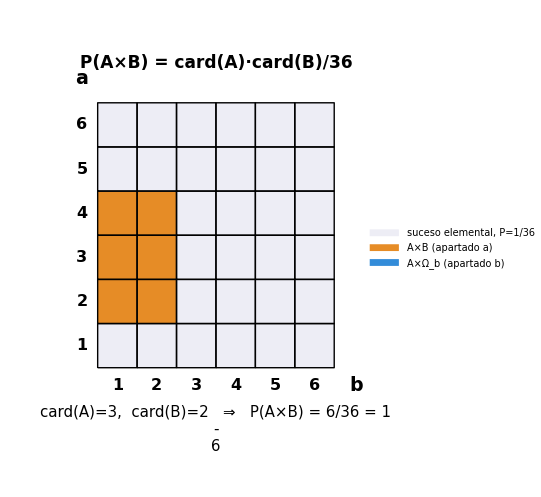
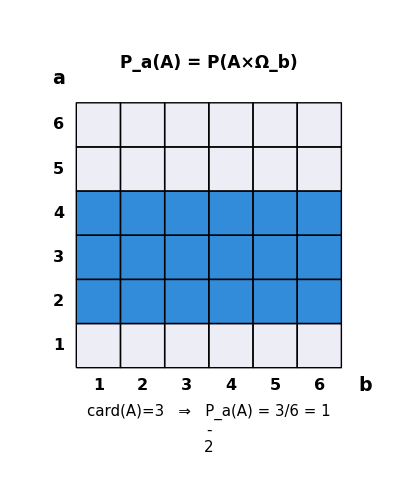

```mathematica
nCaras=6;
A={2,3,4};   (*subconjunto de resultados del dado a,usado como ejemplo*)
Bset={1,2};   (*subconjunto de resultados del dado b,usado como ejemplo*)

colorBase=RGBColor[0.93,0.93,0.96];
colorEvento=RGBColor[0.9,0.55,0.15];
colorMarginal=RGBColor[0.2,0.55,0.85];

cardA=Length[A];
cardB=Length[Bset];
pEvento=(cardA cardB)/36;
pMarginal=cardA/nCaras;

celda[i_,j_,resaltada_,color_]:={If[resaltada,color,colorBase],EdgeForm[{Black,Thickness[0.0025]}],Rectangle[{j-1,i-1},{j,i}]};

ejesGrilla[titulo_,subtitulo_]:={Table[Text[Style[j,16,Bold],{j-0.5,-0.4}],{j,1,nCaras}],Table[Text[Style[i,16,Bold],{-0.4,i-0.5}],{i,1,nCaras}],Text[Style["b",19,Bold],{nCaras+0.55,-0.4}],Text[Style["a",19,Bold],{-0.4,nCaras+0.55}],Text[Style[titulo,17,Bold],{nCaras/2.,nCaras+0.9}],Text[Style[subtitulo,15],{nCaras/2.,-1.4}]};

(*---Panel 1 (apartado a):el rectángulo A x B---*)
gridA=Table[celda[i,j,MemberQ[A,i]&&MemberQ[Bset,j],colorEvento],{i,1,nCaras},{j,1,nCaras}];

subt1="card(A)="<>ToString[cardA]<>",  card(B)="<>ToString[cardB]<>"   ⇒   P(A×B) = "<>ToString[cardA*cardB]<>"/36 = "<>ToString[pEvento];

panel1=Graphics[{gridA,ejesGrilla["P(A×B) = card(A)·card(B)/36",subt1]},PlotRange->{{-0.9,nCaras+0.5},{-1.9,nCaras+1.3}},ImageSize->400];

(*---Panel 2 (apartado b):la marginal A x Omega_b---*)
gridB=Table[celda[i,j,MemberQ[A,i],colorMarginal],{i,1,nCaras},{j,1,nCaras}];

subt2="card(A)="<>ToString[cardA]<>"   ⇒   P_a(A) = "<>ToString[cardA]<>"/6 = "<>ToString[pMarginal];

panel2=Graphics[{gridB,ejesGrilla["P_a(A) = P(A×Ω_b)",subt2]},PlotRange->{{-0.9,nCaras+0.5},{-1.9,nCaras+1.3}},ImageSize->400];

grafico=Row[{panel1,Spacer[40],panel2}];

imagenFinal=Legended[grafico,SwatchLegend[{colorBase,colorEvento,colorMarginal},{"suceso elemental, P=1/36","A×B  (apartado a)","A×Ω_b  (apartado b)"},LabelStyle->Directive[FontSize->16],LegendMarkerSize->20]];

imagenFinal
```

```mathematica
Export["prob_quesada_2_5_a.png",imagenFinal,Background->None,ImageResolution->600];
```